```mathematica
$Assumptions={Element[{ω, B, T},Reals]};
(* Just some pulse definitions *)
nhat = {0, 1, 0};
σ = {PauliMatrix[1], PauliMatrix[2], PauliMatrix[3]};
P4 = MatrixExp[-ⅈ*θ/2 * nhat.σ]/.θ->π/4;
P8 = MatrixExp[-ⅈ*θ/2 * nhat.σ]/.θ->π/8;
mP4 = MatrixExp[ⅈ*θ/2 * nhat.σ]/.θ->π/4;
P2 = MatrixExp[-ⅈ*θ/2 * nhat.σ]/.θ->π/2;
XSMALL = MatrixExp[-ⅈ* ϵ/2  * PauliMatrix[1]];

(* Setting T and B to unity, since they don't matter for this analysis *)
T = 1;
B = 1;
plus = 1/Sqrt[2] * {{1,1}};

(* Defining the free evolution unitary *)
Theta[t2_,t1_]:= Sin[ω*t2]/ω - Sin[ω*t1]/ω;
U[t2_, t1_] := MatrixExp[-ⅈ*B*PauliMatrix[3]*Theta[t2, t1]];
Dagger[X_] := Refine[Conjugate[Transpose[X]], {θ ∈ Reals, ω ∈ Reals}];

(* We'll assume everything is equally spaced, this is technically wlog since you can alwayas consider a longer sequence...*)
(* Produces the associated Z string unitary on the jth pulse*)
Zj[Ps_, j_] :=   Module[{list= Ps,a},a=Length[list];
rtn = PauliMatrix[4];
For[i=1,i<a + 1,i++,rtn=U[T/a*(i), T/a*(i-1)].list[[i]].rtn;
If[ i == j, rtn = PauliMatrix[3].rtn]];
rtn];

(* See the overleaf document. Strings with two Z's in them. *)
Vij[Ps_, i_, j_] := plus.Dagger[Zj[Ps, i]].Zj[Ps, j].Transpose[plus]//FullSimplify;

(* A Z expectation after j pulses, see the overleaf *)
Vijk[Ps_, i_, j_, k_]:=  
Module[{list= Ps,a},a=Length[list];
rtn = PauliMatrix[4];
For[l=1,l<=2*a,l++,
If[l ≤ a, rtn =list[[l]].rtn];
If[l == i, rtn=PauliMatrix[3].rtn];
If[l==2*a -(j-1),  rtn=PauliMatrix[3].rtn];
If[l==k, rtn=PauliMatrix[3].rtn];
If[l> a, rtn =ConjugateTranspose[list[[2*a -l + 1]]].rtn]];
plus.rtn.ConjugateTranspose[plus]]
```

```mathematica
Ps  = {P8,  P2, P8,XSMALL, P2, P2, P4,P8,  P2, P8,XSMALL, P2, P2, P4}/.ϵ->2
Sum[Vijk[Ps, 1, 2, k], {k, 2*Length[Ps]}]//N
```

{{{Cos[π/16],-Sin[π/16]},{Sin[π/16],Cos[π/16]}},{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}},{{Cos[π/16],-Sin[π/16]},{Sin[π/16],Cos[π/16]}},{{Cos[1],-ⅈ Sin[1]},{-ⅈ Sin[1],Cos[1]}},{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}},{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}},{{Cos[π/8],-Sin[π/8]},{Sin[π/8],Cos[π/8]}},{{Cos[π/16],-Sin[π/16]},{Sin[π/16],Cos[π/16]}},{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}},{{Cos[π/16],-Sin[π/16]},{Sin[π/16],Cos[π/16]}},{{Cos[1],-ⅈ Sin[1]},{-ⅈ Sin[1],Cos[1]}},{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}},{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}},{{Cos[π/8],-Sin[π/8]},{Sin[π/8],Cos[π/8]}}}

{{-2.20692-2.58715 ⅈ}}

```mathematica
Vijk[Ps, 2, 3, 9]//N
```

{{0.159252+0.909297 ⅈ}}

```mathematica
plus
```

{{1/(√2),1/(√2)}}

```mathematica
Ps  = { P4, P2, P2, P2,  P2, P2, P2}
```

{{{Cos[π/8],-Sin[π/8]},{Sin[π/8],Cos[π/8]}},{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}},{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}},{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}},{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}},{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}},{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}}}

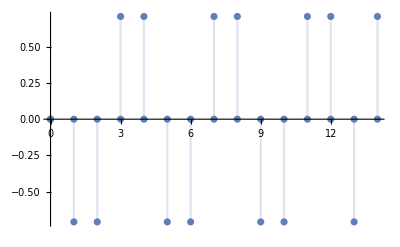

```mathematica
Show[DiscretePlot[Re[Vijk[Ps, 1, 2, k]][[1]][[1]], {k,0, 2*Length[Ps]}], DiscretePlot[Im[Vijk[Ps, 1, 2, k]][[1]][[1]], {k,0, 2*Length[Ps]}]]
```

```mathematica
Re[Vijk[Ps, 1, 2, 4]]//N
```

{{1.}}

```mathematica
Sum[Vijk[Ps, 2, 4, k], {k, 2*Length[Ps]}]//N
```

{{2.82843}}

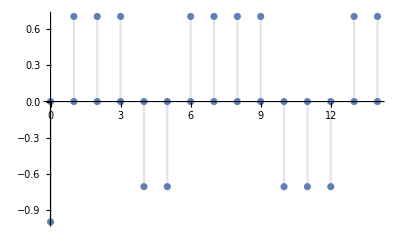

```mathematica
Show[DiscretePlot[Re[Vijk[Ps, 2, 4, k]][[1]][[1]], {k,0, 2*Length[Ps]}], DiscretePlot[Im[Vijk[Ps, 2, 4, k]][[1]][[1]], {k,0, 2*Length[Ps]}]]
```

```mathematica
Ps  = { P4, P2, P2, P2,  P2, P2, P2}
```

```mathematica
Vi[Ps_, i_]:=  
Module[{list= Ps,a},a=Length[list];
rtn = PauliMatrix[4];
For[l=1,l<=2*a,l++,
If[l ≤ a, rtn =list[[l]].rtn];
If[l == i, rtn=PauliMatrix[3].rtn];
If[l> a, rtn =ConjugateTranspose[list[[2*a -l + 1]]].rtn]];
plus.rtn.ConjugateTranspose[plus]]
Sum[Vi[Ps, k], {k, 2*Length[Ps]}]//N
```

{{-1.41421}}

```mathematica
Vij[Ps_, i_, j_]:=  
Module[{list= Ps,a},a=Length[list];
rtn = PauliMatrix[4];
For[l=1,l<=2*a,l++,
If[l ≤ a, rtn =list[[l]].rtn];
If[l == i, rtn=PauliMatrix[3].rtn];
If[l==j, rtn=PauliMatrix[3].rtn];
If[l> a, rtn =ConjugateTranspose[list[[2*a -l + 1]]].rtn]];
plus.rtn.ConjugateTranspose[plus]]
```

```mathematica
Sum[Vij[Ps, 1,  k], {k, 2*Length[Ps]}]//N
```

$Aborted

```mathematica
Vijk[Ps_, i_, j_, k_]:=  
Module[{list= Ps,a},a=Length[list];
rtn = PauliMatrix[4];
For[l=1,l<=2*a,l++,
If[l ≤ a, rtn =list[[l]].rtn];
If[l == i, rtn=PauliMatrix[3].rtn];
If[l==j, rtn=PauliMatrix[3].rtn];
If[l==k, rtn=PauliMatrix[3].rtn];
If[l> a, rtn =ConjugateTranspose[list[[2*a -l + 1]]].rtn]];
plus.rtn.ConjugateTranspose[plus]]
```